```mathematica
(*1. Генерация статистических данных (11 интервалов)*)
n = 11;
t = RandomVariate[ExponentialDistribution[0.033],n];
Print["t=",t=Sort[t]];
```

t={10.571,22.335,23.8208,24.0536,27.9216,32.5172,40.6017,41.1338,47.4282,80.9589,129.045}

```mathematica
(*2. Решение системы уравнений и нахождение коэффициентов*)
sol=N[Solve[Sum[(1/(E01-i+1))- Kjm1* Part[t,i],{i,1,n}]== 0 && 
Sum[(1/(Kjm1))- (E01-i+1)* Part[t,i],{i,1,n}]== 0 ,{E01,Kjm1},Reals]];
Answer = Cases[{Kjm1,E01}/.sol,{_?Positive,_}];
Print["Kjm=",Kjm =Last[Answer][[1]]];
Print["E0=",E0 = Last[Answer][[2]]];
```

Kjm=0.00496706

E0=11.5762

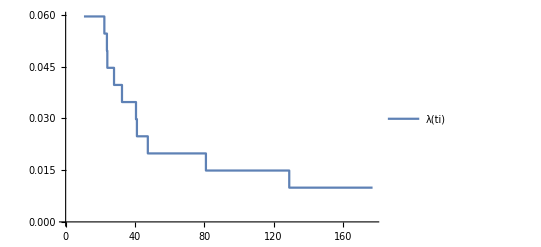

```mathematica
(*3. Рассчет параметров модели*)
λ = {};
For[i=1,i≤n,i++,AppendTo[λ,Kjm*(Ceiling[E0]-(i-1))]];
Matr ={};
For[i=1,i≤n,i++,AppendTo[Matr,{Part[t,i],Part[λ ,i]}]];
ListStepPlot[Legended[Matr,"λ(ti)"]]
```

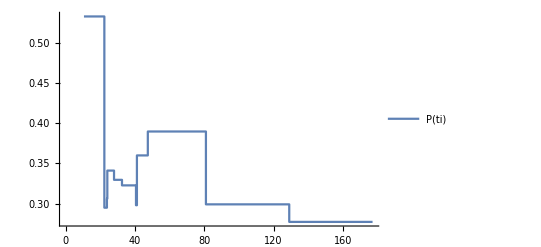

```mathematica
P = {};
For[i=1,i≤n,i++,AppendTo[P,Exp[-Part[λ,i]*Part[t,i]]]];
Matr ={};
For[i=1,i≤n,i++,AppendTo[Matr,{Part[t,i],Part[P ,i]}]];
ListStepPlot[Legended[Matr,"P(ti)"]]
```

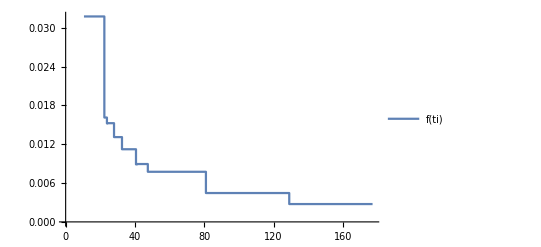

```mathematica
f = {};
For[i=1,i≤n,i++,AppendTo[f,Part[λ,i]*Exp[-Part[λ,i]*Part[t,i]]]];
Matr ={};
For[i=1,i≤n,i++,AppendTo[Matr,{Part[t,i],Part[f ,i]}]];
ListStepPlot[Legended[Matr,"f(ti)"]]
```

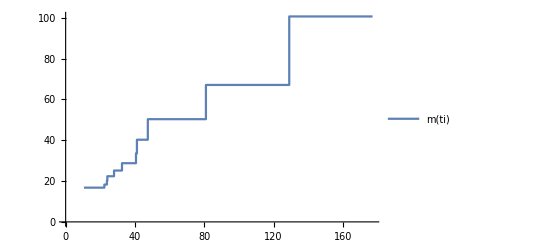

```mathematica
m = {};
For[i=1,i≤n,i++,AppendTo[m,1/Part[λ,i]]];
Matr ={};
For[i=1,i≤n,i++,AppendTo[Matr,{Part[t,i],Part[m,i]}]];
ListStepPlot[Legended[Matr,"m(ti)"]]
```

```mathematica
Print["λ(t12)=",λt12= Kjm*(Ceiling[E0]-n )];
Print["m(t12)=", mt12=1/λt12];
Print["P(t12)=", TraditionalForm[Pt12 = Exp[-λt12*t12]]];
```

λ(t12)=0.00496706

m(t12)=201.326

P(t12)=ⅇ^(-0.00496706 t12)